| Estimate | Standard Error | t-Statistic | P-Value
μ | 90.6847 | 0.142687 | 635.55 | 1.36843×10^-30
σ | 3.68714 | 0.159966 | 23.0495 | 6.29443×10^-12
k | 17065.8 | 596.737 | 28.5986 | 4.01081×10^-13

1846.49 ⅇ^(-0.0367783 (-90.6847+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
μ | 232.427 | 0.113925 | 2040.17 | 9.81138×10^-50
σ | 7.21638 | 0.143789 | 50.1872 | 8.48408×10^-21
k | 82288.2 | 1285.36 | 64.0195 | 1.08602×10^-22

4549.13 ⅇ^(-0.00960132 (-232.427+x)^2)

{μ→90.6847,σ→3.68714,k→17065.8}

{μ→232.427,σ→7.21638,k→82288.2}

FittedModel[-369.373+4.43595 x]

{32.9,38.5154}

{661.66,75.3814}

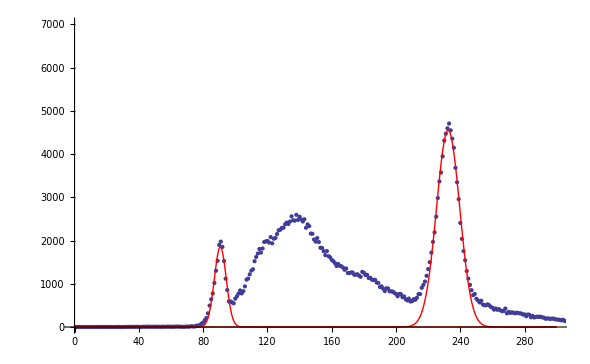

```mathematica
(*Clear unused stuff*)
Clear[ Filename, Filepath, rawBackground, rawData, BackgroundTime, DataTime, removeBackground];

type = "Na";

(*Specify folder structure and filenames*)
Filename = If[type=="Na","Na22-no-bg", "Cs137-1-no-bg"];
Filepath = NotebookDirectory[]<>"../data/";

(*Import raw data from .Spe files*)
rawData = Import[Filepath<> Filename <>".txt", "Table"];
cutData = rawData;

xraypeak = Take[cutData, If[type=="Na", {140,150}, {80,95}]];
gammapeak = Take[cutData, If[type=="Na", {230,245}, {220,240}]];

model[x_] =k*Exp[-1/2 ((x-μ)/σ)^2]/(σ √(2 π));

xrayfitModel=NonlinearModelFit[xraypeak, model[x], {{μ, If[type=="Na",140, 90]}, {σ, 4}, {k, 20000}}, x];
gammafitModel=NonlinearModelFit[gammapeak, model[x], {{μ, 220}, {σ, 8}, {k, 90000}}, x];

xrayfitModel["ParameterTable"]
xrayfitModel["BestFit"]
gammafitModel["ParameterTable"]
gammafitModel["BestFit"]

xrayfit = xrayfitModel["BestFitParameters"]
gammafit = gammafitModel["BestFitParameters"] 
xrayTeX = model[x]/.xrayfit;
gammaTeX = model[x]/.gammafit;

ExportString[xrayTeX, "TeX"];
ExportString[gammaTeX, "TeX"];

(* Energy Calibration *)
lit1 =If[type=="Na",511, 32.9];
lit2 =If[type=="Na",1275, 661.66];
DataSet ={{Last[First[xrayfit]], lit1}, {Last[First[gammafit]], lit2}};
calibration=LinearModelFit[DataSet,x,x]

{xrayfitModel["BestFitParameters"][[1]] [[2]]* calibration["BestFitParameters"][[2]]+calibration["BestFitParameters"][[1]], xrayfitModel["BestFitParameters"][[2]] [[2]]*2.35482 * calibration["BestFitParameters"][[2]]}

{gammafitModel["BestFitParameters"][[1]] [[2]]* calibration["BestFitParameters"][[2]] + calibration["BestFitParameters"][[1]],gammafitModel["BestFitParameters"][[2]] [[2]]*2.35482 * calibration["BestFitParameters"][[2]]}

exportName ="Na22-sum-no-bg";
dataToCalibrate = Import[Filepath<> exportName <>".txt", "Table"];
calibratedDate = Select[{calibration[First[#]], Last[#]}&/@dataToCalibrate,First[#]≥-900&];
(*Export[Filepath<> exportName <>"-calibrated.txt", calibratedDate, "Table"];*)


Show[{ListPlot[cutData, PlotRange->{{0,300}, {0, 7000}}], Plot[ model[x]/.xrayfit,  {x,0,300}, PlotStyle->Red, PlotRange->{{0,300}, {0, 7000}}],Plot[ model[x]/.gammafit,  {x,0,300}, PlotStyle->Red, PlotRange->{{0,300}, {0, 7000}}]}]
```